## Using PRIMAT to estimate uncertainty on rates using a Monte-Carlo

### Loading PRIMAT

Setting the notebook directory (in batch mode this is not evaluated because it seems to be the default one)

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we go the parent directory, or base directory of PRIMAT.

```mathematica
SetDirectory[ParentDirectory[Directory[]]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

We load PRIMAT. It takes some time because it starts reading the file with nuclear reactions and deduces which are the nuclides needed, 
and it starts to build formally the network of equations

```mathematica
Timing[<<PRIMAT-Main.m]
```

{16.2009,Null}

### Launch MC

```mathematica
$ParallelBool=True;
MachineNumerics=""(*$MachineName*);
```

Let us run a Monte Carlo with LengthMC points. Possibly with parallelization if the corresponding option $ParallelBool is set to True.

```mathematica
LengthMC=10;(* should put 1000 or 10000 *)
```

We decide if we randomize on baryons and neutron lifetime

```mathematica
$Randomh2Ωb=False;
$Randomτneutron=True;
$RandomNuclearRates=True;
```

```mathematica
AbsoluteTiming[RunPRIMATMonteCarlo[LengthMC];];
DumpMC[MachineNumerics<>"NuclearNeutron"];
```

Running a Monte-Carlo with 10 points.

Number of Kernels 2

Iteration 1  Memory usage = 54569088 time = 63.6181  Kernel : 2

Iteration 4  Memory usage = 54677704 time = 64.127  Kernel : 1

Iteration 2  Memory usage = 54733312 time = 66.2  Kernel : 2

Iteration 5  Memory usage = 54604816 time = 65.8025  Kernel : 1

Iteration 3  Memory usage = 54695888 time = 69.8716  Kernel : 2

Iteration 6  Memory usage = 54851520 time = 70.2832  Kernel : 1

Iteration 7  Memory usage = 54819992 time = 66.2869  Kernel : 2

Iteration 9  Memory usage = 54883664 time = 67.7233  Kernel : 1

Iteration 8  Memory usage = 54795976 time = 68.1481  Kernel : 2

Iteration 10  Memory usage = 54640064 time = 67.1016  Kernel : 1

Exporting MonteCarlo/MCNuclearNeutron.dat

Exporting MonteCarlo/RVNuclearNeutron.dat

Exporting MonteCarlo/CosmoNuclearNeutron.dat

We dumped the results on the harddisk so as to be able to analyze it later 
The file starting with MC is the list of abundances at the end of BBN for all species and for all points of the Monte-Carlo. 
The RV file is the list of random variables used to generate the reaction rates.
The Cosmo file is the list of cosmological parameters (h^2 Ω_b0,τ_neutron).

### Results

We can import the results of the Monte-Carlo analysis made on a different computer or earlier and that we have dumped on harddisk.

```mathematica
MachineOfRuns="";
```

```mathematica
LoadMC[MachineOfRuns<>"NuclearNeutron"]
```

We check that we have many (10 000?) points for the 59 nuclides

```mathematica
Dimensions[MC]
```

{10,59}

We work with log(quantities) so as to relate relative variations

```mathematica
YP:=4*ElementColumn["a"]
DH:=10^5 ElementColumn["d"]/ElementColumn["p"]
LogY:=Log[4*ElementColumn["a"]]
LogDoverH:=Log[10^5 ElementColumn["d"]/ElementColumn["p"]]
LogHe3overH:=Log[10^5(ElementColumn["He3"]+ElementColumn["t"])/ElementColumn["p"]]
LogLi7overH:=Log[10^10(ElementColumn["Li7"]+ElementColumn["Be7"])/ElementColumn["p"]]
Logτ:=Log@τneutronList
LogBaryons:=Log@h2Ωb0List
```

Averages and standard deviation

```mathematica
MeanthYHe=Mean[Exp@LogY]
σthYHe=StandardDeviation[Exp@LogY]
MeanthDH=Mean[Exp@LogDoverH]
σthDH=StandardDeviation[Exp@LogDoverH]
```

0.24716

0.000302229

2.4681

0.031562

Correlations

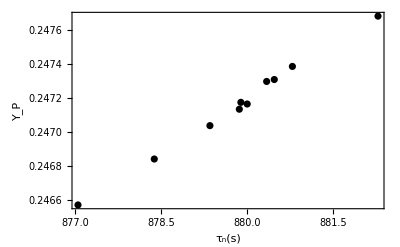

```mathematica
YpEtaMC=ListPlot[Transpose[{Exp@Logτ,Exp@LogY}],Frame->True,FrameLabel->{"τ_n(s)","Y_P"},PlotStyle->Black]
```

Estimation of δ ln Y_P/δ ln τ_n and idem for D/H, He3/H and Li7/H.

```mathematica
Sτ=StandardDeviation[Logτ]
SB=StandardDeviation[LogBaryons]
```

0.0015909

9.36222×10^-16

Dependence wrt to τ_neutron

```mathematica
Covariance[LogY,Logτ]/Sτ^2
Covariance[LogDoverH,Logτ]/Sτ^2
Covariance[LogHe3overH,Logτ]/Sτ^2
Covariance[LogLi7overH,Logτ]/Sτ^2
```

0.766998

-3.02485

-6.51815

-3.78277

Observed values for Y_P

```mathematica
σObsYHeCorrect=0.0040;
YHeobsCorrect=0.2449;

σObsYHeWrong=0.0022;
YHeobsWrong=0.2551;
```

```mathematica
YHeobs=YHeobsCorrect;
σObsYHe=σObsYHeCorrect;
```

Observed value for D/H

```mathematica
σObsDH=0.030;
YDHObs=2.527;
```

Posterior of baryons from CMB

```mathematica
Meanh2Ωb0
σh2Ωb0
```

0.02225

0.00016

```mathematica
PostCMB[h2Ωb0_]:=With[{δh2Ωb0=h2Ωb0-Meanh2Ωb0},1/(√(2π)σh2Ωb0)Exp[(-(δh2Ωb0)^2)/(2 σh2Ωb0^2)]];
```

Lower, median & upper quantiles.

We take the values corresponding to 16%, 50% and 84% of Monte-Carlo runs (Because for a Gaussian one sigma corresponds to 68% so 0.16 - 0.84 range takes indeed 68%). 
These can be used to estimate the uncertainty in the abundance predictions.

Useful quantiles

```mathematica
(1-0.6827)/2
(1-0.9545)/2
```

0.15865

0.02275

```mathematica
1-0.15865
1-0.02275
```

0.84135

0.97725

Quantiles for most important isotopes, Mean, and σ/mean

Y_P

```mathematica
4Quantile[TMC[[KeyVal["a"]]],{0.02275,0.15865,0.5,1-0.15865,1-0.02275}]
4Mean@TMC[[KeyVal["a"]]]
4StandardDeviation@TMC[[KeyVal["a"]]]
4StandardDeviation@TMC[[KeyVal["a"]]]/%%
```

{0.246574,0.246843,0.247165,0.247385,0.24768}

0.24716

0.000302229

0.00122281

10^5D/H

```mathematica
Quantile[10^5TMC[[KeyVal["d"]]]/TMC[[KeyVal["p"]]],{0.02275,0.15865,0.5,1-0.15865,1-0.02275}]
Mean[10^5TMC[[KeyVal["d"]]]/TMC[[KeyVal["p"]]]]
StandardDeviation[10^5TMC[[KeyVal["d"]]]/TMC[[KeyVal["p"]]]]
StandardDeviation[10^5TMC[[KeyVal["d"]]]/TMC[[KeyVal["p"]]]]/%%
```

{2.41251,2.42462,2.46955,2.49661,2.50149}

2.4681

0.031562

0.0127879

10^5 He3/H

```mathematica
Quantile[10^5(TMC[[KeyVal["He3"]]]+TMC[[KeyVal["t"]]])/TMC[[KeyVal["p"]]],{0.02275,0.15865,0.5,1-0.15865,1-0.02275}]
Mean[10^5(TMC[[KeyVal["He3"]]]+TMC[[KeyVal["t"]]])/TMC[[KeyVal["p"]]]]
StandardDeviation[10^5(TMC[[KeyVal["He3"]]]+TMC[[KeyVal["t"]]])/TMC[[KeyVal["p"]]]]
StandardDeviation[10^5(TMC[[KeyVal["He3"]]]+TMC[[KeyVal["t"]]])/TMC[[KeyVal["p"]]]]/%%
```

{1.04534,1.05544,1.07599,1.09231,1.09765}

1.07401

0.0166701

0.0155214

10^10Li7/H

```mathematica
Quantile[10^10(TMC[[KeyVal["Li7"]]]+TMC[[KeyVal["Be7"]]])/TMC[[KeyVal["p"]]],{0.02275,0.15865,0.5,1-0.15865,1-0.02275}]
Mean[10^10(TMC[[KeyVal["Li7"]]]+TMC[[KeyVal["Be7"]]])/TMC[[KeyVal["p"]]]]
StandardDeviation[10^10(TMC[[KeyVal["Li7"]]]+TMC[[KeyVal["Be7"]]])/TMC[[KeyVal["p"]]]]
StandardDeviation[10^10(TMC[[KeyVal["Li7"]]]+TMC[[KeyVal["Be7"]]])/TMC[[KeyVal["p"]]]]/%%
```

{5.30794,5.4135,5.55289,5.79872,5.94703}

5.62294

0.205982

0.0366325

10^14Li6/H

```mathematica
Quantile[10^14(TMC[[KeyVal["Li6"]]])/TMC[[KeyVal["p"]]],{0.02275,0.15865,0.5,1-0.15865,1-0.02275}]
Mean[10^14(TMC[[KeyVal["Li6"]]])/TMC[[KeyVal["p"]]]]
StandardDeviation[10^14(TMC[[KeyVal["Li6"]]])/TMC[[KeyVal["p"]]]]/%
```

{1.03516,1.23207,1.39884,1.94475,2.58167}

1.55537

0.282447

10^15CNO/H

```mathematica
Quantile[10^15(Plus@@(TMC[[KeyVal[#]]]&/@CNONuclei))/TMC[[KeyVal["p"]]],{0.02275,0.15865,0.5,1-0.15865,1-0.02275}]
Mean[10^15(Plus@@(TMC[[KeyVal[#]]]&/@CNONuclei))/TMC[[KeyVal["p"]]]]
StandardDeviation[10^15(Plus@@(TMC[[KeyVal[#]]]&/@CNONuclei))/TMC[[KeyVal["p"]]]]/%
```

{0.0237499,0.0523962,0.563671,1.53089,1.54696}

0.778669

0.772659